```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\Dropbox\UNI\Projekte\A02_MCWD_Dataset_Analysis\2021\Analysis\Figure3

```mathematica
dataAgree05010=Import["2005-2010Agreement.tsv"];
dataAgree16=Import["2016Agreement.tsv"];
```

```mathematica
dataAgree16
```

{{,Year,Dataset,Condition,TotalArea,RelativeArea},{0,2016,CHIRPS,0,1.16974×10^6,0.196776},{0,2016,CRU NCEP,0,1.32103×10^6,0.222227},{0,2016,ERA 5,0,979376.,0.164752},{0,2016,GLDAS,0,817446.,0.137512},{0,2016,TRMM 7,0,801601.,0.134847},{0,2016,GPCC,0,427878.,0.0719783},{0,2016,CHIRPS,1,1.56946×10^6,0.264017},{0,2016,CRU NCEP,1,474077.,0.0797501},{0,2016,ERA 5,1,348084.,0.0585553},{0,2016,GLDAS,1,314915.,0.0529755},{0,2016,TRMM 7,1,89584.4,0.01507},{0,2016,GPCC,1,12359.7,0.00207917},{0,2016,CHIRPS,2,1.27587×10^6,0.214629},{0,2016,CRU NCEP,2,366961.,0.0617308},{0,2016,ERA 5,2,160437.,0.026989},{0,2016,GLDAS,2,89593.5,0.0150716},{0,2016,TRMM 7,2,6179.86,0.00103959},{0,2016,GPCC,2,3089.81,0.000519774}}

```mathematica
scens05010 = DeleteDuplicates[Rest[dataAgree05010[[All,3]]]]
```

{CHIRPS,CRU NCEP,ERA 5,GLDAS,GPCC,TRMM 6,TRMM 7,GSWP 3,WATCH WFDEI}

```mathematica
scens16 = DeleteDuplicates[Rest[dataAgree16[[All,3]]]]
```

{CHIRPS,CRU NCEP,ERA 5,GLDAS,TRMM 7,GPCC}

```mathematica
Length@scens05010
```

9

```mathematica
Length@scens16
```

6

```mathematica
cols[2010] =cols[2005]=  Table[Blend[{Orange, Darker@Green, Darker@Blue},i],{i,0, 1,1/(Length@scens05010-1)}]
```

{RGBColor[1, 0.5, 0],RGBColor[Rational[3, 4], 0.5416666666666666, 0],RGBColor[Rational[1, 2], 0.5833333333333333, 0],RGBColor[Rational[1, 4], 0.625, 0],RGBColor[0, Rational[2, 3], 0],RGBColor[0, Rational[1, 2], Rational[1, 6]],RGBColor[0, Rational[1, 3], Rational[1, 3]],RGBColor[0, Rational[1, 6], Rational[1, 2]],RGBColor[0, 0, Rational[2, 3]]}

```mathematica
cols[2016]=  Table[Blend[{Orange, Darker@Green, Darker@Blue},i],{i,0, 1,1/(Length@scens16-1)}]
```

{RGBColor[1, 0.5, 0],RGBColor[Rational[3, 5], 0.5666666666666667, 0],RGBColor[Rational[1, 5], 0.6333333333333333, 0],RGBColor[0, Rational[8, 15], Rational[2, 15]],RGBColor[0, Rational[4, 15], Rational[2, 5]],RGBColor[0, 0, Rational[2, 3]]}

```mathematica
agreeData[2005] = Partition[Select[dataAgree05010,#[[2]]==2005&][[All,6]],9]*100
```

{{10.442,10.5266,7.94964,4.76185,5.38255,5.81989,6.38669,10.9254,15.5946},{8.39304,3.7158,4.44021,2.83296,1.64761,0.8785,0.309572,1.08731,0.414296},{3.30525,0.930548,0.828463,0.155513,0.414106,0.569915,0.207245,0.259123,0.0518033}}

```mathematica
agreeData[2010] = Partition[Select[dataAgree05010,#[[2]]==2010&][[All,6]],9]*100
```

{{6.00792,9.02473,9.88034,10.8399,9.77596,8.31147,9.37481,12.1844,20.654},{22.5377,10.4264,3.93264,3.76144,1.80055,0.829367,0.354956,0.353547,0.},{12.4621,1.91816,1.08972,1.76326,0.415059,0.207462,0.,0.,0.}}

```mathematica
agreeData[2016] = Partition[Select[dataAgree16,#[[2]]==2016&][[All,6]],6]*100
```

{{19.6776,22.2227,16.4752,13.7512,13.4847,7.19783},{26.4017,7.97501,5.85553,5.29755,1.507,0.207917},{21.4629,6.17308,2.6989,1.50716,0.103959,0.0519774}}

```mathematica
mcwdClasses = {moderate, severe, exterme}
```

{moderate,severe,exterme}

```mathematica
years = {2005, 2010, 2016}
```

{2005,2010,2016}

```mathematica
Reverse[Accumulate[Reverse[agreeData[2005][[1]]]]]
```

{62.1946,51.7526,41.226,33.2764,28.5145,23.132,17.3121,10.9254}

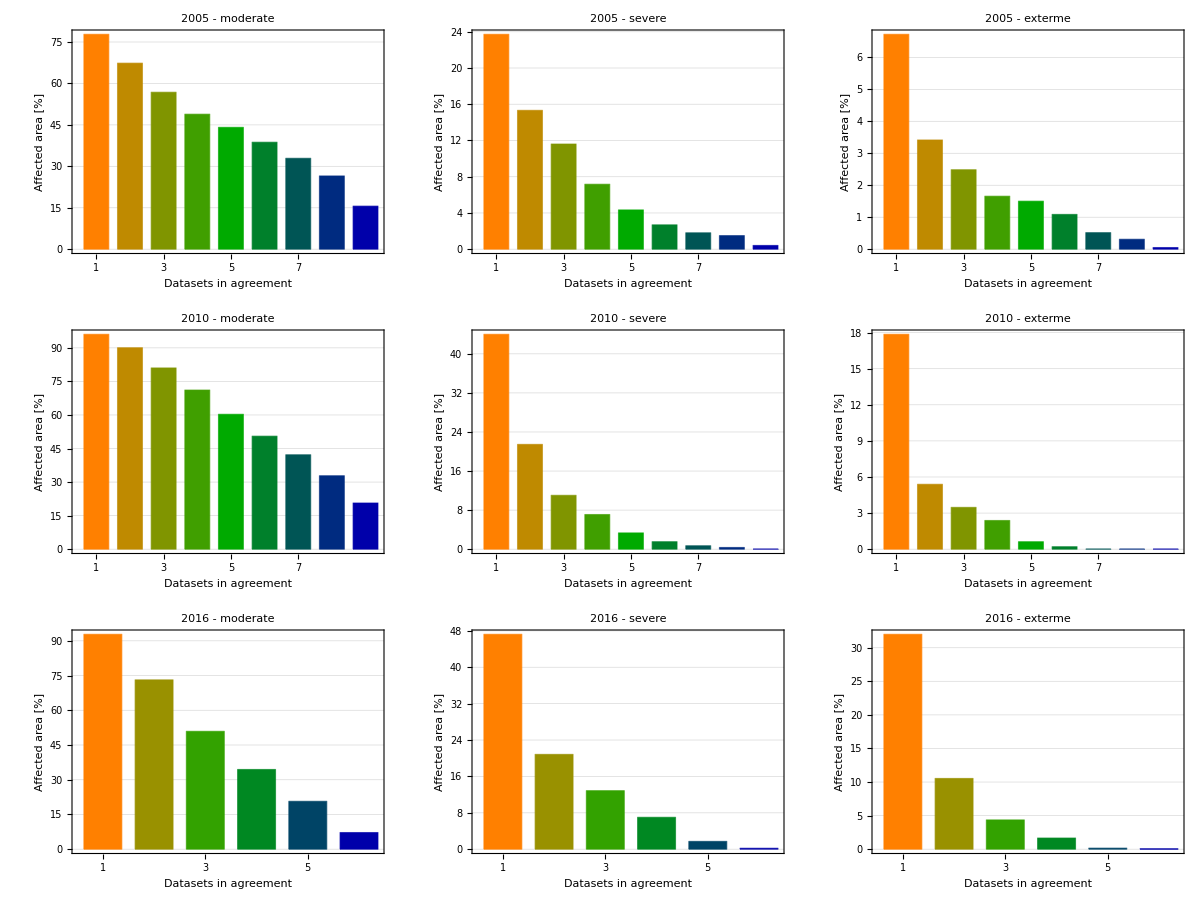

```mathematica
Grid[Table[BarChart[Reverse[Accumulate[Reverse[agreeData[year][[c]]]]],ChartLabels->{scens05010, Range[8]}, LabelStyle->Directive[12, Black, FontFamily->"Arial"], BarSpacing->0.35, ChartStyle->cols[year],  FrameLabel->{"Datasets in agreement","Affected area [%]"}, Frame->True, PlotLabel-> ToString@year<> " - "<> ToString@mcwdClasses[[c]], PlotRange->100, ImageSize->300, GridLines->Automatic], {year,years},{c,1,3}]]
```

```mathematica
TableForm[Table[Reverse[Round[Accumulate[Reverse[agreeData[year][[c]]]]/100*5.94, 0.1]],{year,years} ,{c, 1,3}], TableHeadings->{years, mcwdClasses}]
```

| moderate | severe | exterme
2005 | 4.6
4.
3.4
2.9
2.6
2.3
2.
1.6
0.9 | 1.4
0.9
0.7
0.4
0.3
0.2
0.1
0.1
0. | 0.4
0.2
0.1
0.1
0.1
0.1
0.
0.
0.
2010 | 5.7
5.3
4.8
4.2
3.6
3.
2.5
2.
1.2 | 2.6
1.3
0.7
0.4
0.2
0.1
0.
0.
0. | 1.1
0.3
0.2
0.1
0.
0.
0.
0.
0.
2016 | 5.5
4.3
3.
2.
1.2
0.4 | 2.8
1.2
0.8
0.4
0.1
0. | 1.9
0.6
0.3
0.1
0.
0.

```mathematica
TableForm[Table[Reverse[Round[Accumulate[Reverse[agreeData[year][[c]]]], 0.1]],{year,years} ,{c, 1,3}], TableHeadings->{years, mcwdClasses}, Frame->All]
```

| moderate | severe | exterme
2005 | 77.8
67.3
56.8
48.9
44.1
38.7
32.9
26.5
15.6 | 23.7
15.3
11.6
7.2
4.3
2.7
1.8
1.5
0.4 | 6.7
3.4
2.5
1.7
1.5
1.1
0.5
0.3
0.1
2010 | 96.1
90.
81.
71.1
60.3
50.5
42.2
32.8
20.7 | 44.
21.5
11.
7.1
3.3
1.5
0.7
0.4
0. | 17.9
5.4
3.5
2.4
0.6
0.2
0.
0.
0.
2016 | 92.8
73.1
50.9
34.4
20.7
7.2 | 47.2
20.8
12.9
7.
1.7
0.2 | 32.
10.5
4.4
1.7
0.2
0.1

```mathematica
Export["barchart.png", dHistograms, ImageResolution-> 300]
```

barchart.png

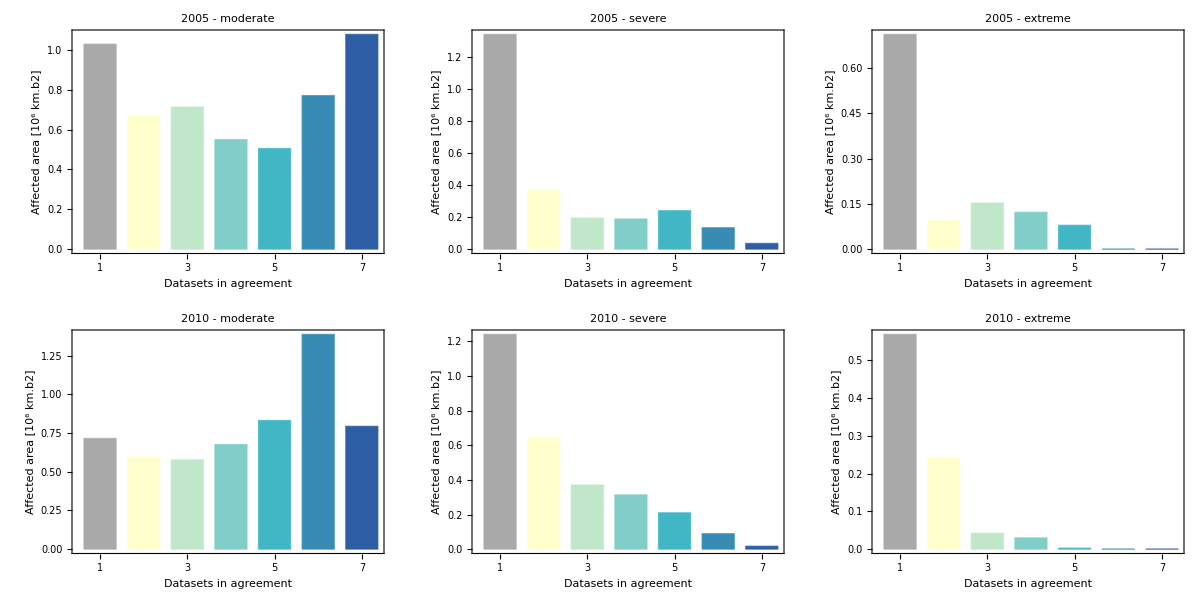

```mathematica
dHistograms2 =Grid[Table[BarChart[dataAgreeSub[j,i],ChartLabels->{scensShort, Range[7]}, LabelStyle->Directive[12, Black, FontFamily->"Arial"], BarSpacing->0.35, ChartStyle->colsArray[[i]], FrameLabel->{"Datasets in agreement","Affected area [10^6 km.b2]"}, Frame->True, PlotLabel-> years[[i]]<> " - "<> mcwdClasses[[j]], PlotRange->1.8, ImageSize->300],{i,1,2} ,{j, 1,3}], Spacings->{0.5,1}]
```

```mathematica
Export["SpatialAgreement05_10.png", dHistograms2, ImageResolution-> 300]
```

SpatialAgreement05_10.png

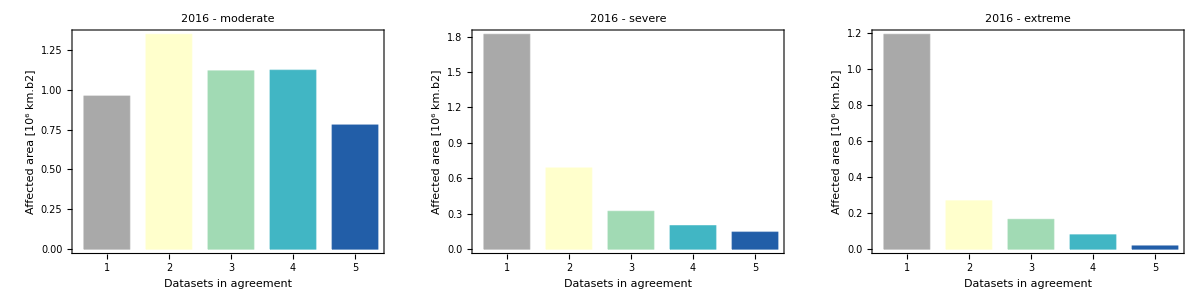

```mathematica
dHistograms3 =Grid[Table[BarChart[dataAgreeSub[j,i],ChartLabels->{scensShort, Range[7]}, LabelStyle->Directive[12, Black, FontFamily->"Arial"], BarSpacing->0.35, ChartStyle->colsArray[[i]], FrameLabel->{"Datasets in agreement","Affected area [10^6 km.b2]"}, Frame->True, PlotLabel-> years[[i]]<> " - "<> mcwdClasses[[j]], PlotRange->1.8, ImageSize->300],{i,3,3} ,{j, 1,3}], Spacings->{0.5,1}]
```

```mathematica
Export["SpatialAgreement16.png", dHistograms3, ImageResolution-> 300]
```

SpatialAgreement16.png

```mathematica
x= 9.9*10^99
```

9.9×10^99

```mathematica
x  = 1.5678
```

1.5678

```mathematica
x  = x^2
```

9.49808×10^199

```mathematica
N[Log10[π^π^π^π],10]
```

6.66262453×10^17